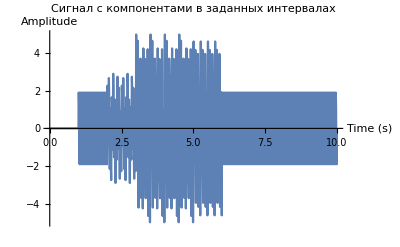

```mathematica
(*1. Исходные параметры*)spec=<|MaxTime->10,SampleRate->100,Components->{<|Amplitude->2,Frequency->20,TStart->1,TEnd->10|>,<|Amplitude->3,Frequency->32,TStart->3,TEnd->6|>,<|Amplitude->1,Frequency->6,TStart->2,TEnd->5|>}|>;

(*2. Генерация сигнала*)
data=Table[{t,Total@Map[If[#[TStart]<=t<=#[TEnd],1,0]*#[Amplitude]*Sin[2 Pi t #[Frequency]]&,spec[Components]]},{t,0,spec[MaxTime],1/spec[SampleRate]}];

(*3. Построение временного графика*)
ListLinePlot[data,PlotRange->All,AxesLabel->{"Time (s)","Amplitude"},PlotLabel->"Сигнал с компонентами в заданных интервалах"]
```

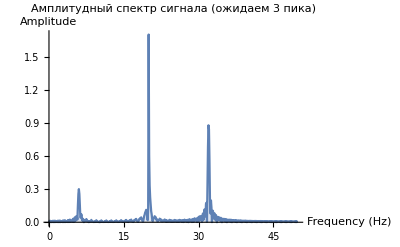

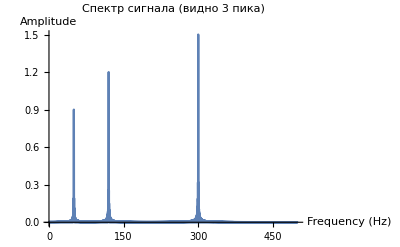

```mathematica
(*4. Выделяем значения амплитуды*)values=data[[All,2]];
n=Length[values];

(*5. Прямое ДПФ*)
fourier=Fourier[values,FourierParameters->{1,-1}];
scaledAmplitude=2*Abs[fourier]/n;

(*6. Частотная сетка*)
freqs=Range[0,n-1]*spec[SampleRate]/n;

(*7. Берем первую половину спектра*)
halfLength=Floor[n/2];
freqsHalf=Take[freqs,halfLength];
amplitudeHalf=Take[scaledAmplitude,halfLength];

(*8. Спектральный график*)
ListLinePlot[Transpose[{freqsHalf,amplitudeHalf}],PlotRange->All,Filling->Axis,AxesLabel->{"Frequency (Hz)","Amplitude"},PlotLabel->"Амплитудный спектр сигнала (ожидаем 3 пика)"]
```